Инициализация данных

```mathematica
numberOfContainers=20;(*кол-во контейнеров*)
numberOfVehicles=3;(*кол-во техники*)
numberOfStacks=2;(*кол-во стеков*)
```

```mathematica
ϵ=0.1;
shareOfPairsBlocks=0.05;
```

```mathematica
(*генерация вершин*)
vertices1=Range@numberOfContainers;
vertices2=vertices1+numberOfContainers;
```

```mathematica
(*генерация матрицы расстояний*)
{pointsVertices1,pointsVertices2}=Table[RandomReal[{1,5},{numberOfContainers,2}],2];
distanceMatrix=DistanceMatrix[pointsVertices1,pointsVertices2];
```

```mathematica
δ1=δ2=Ceiling@Mean@Flatten@distanceMatrix;
```

```mathematica
(*генерация дуг*)
outArcs=MapThread[DirectedEdge,{vertices1,vertices2}];
inArcs=DeleteCases[Flatten[Outer[DirectedEdge,vertices2,vertices1]],i_->j_/;i-numberOfContainers==j];
startArcs=Thread[DirectedEdge[0,vertices1]];
endArcs=Thread[DirectedEdge[vertices2,2numberOfContainers+1]];
arcs=Join[startArcs,inArcs,outArcs,endArcs];
```

```mathematica
(*стеки*)
getVarianteTwoArg=RandomVariate@MultinomialDistribution[#1,ConstantArray[1/#2,#2]]&;


stacks=TakeList[RandomSample@vertices1,getVarianteTwoArg[numberOfContainers,numberOfStacks]];
```

```mathematica
{pairsVertices1,pairsVertices2}=RandomSample[#,Floor[shareOfPairsBlocks Length@#]]&@Subsets[#,{2}]&/@{vertices1,vertices2};
```

```mathematica
K=numberOfVehicles(Total[Max/@distanceMatrix]+Total[Max/@distanceMatrixᵀ]);
```

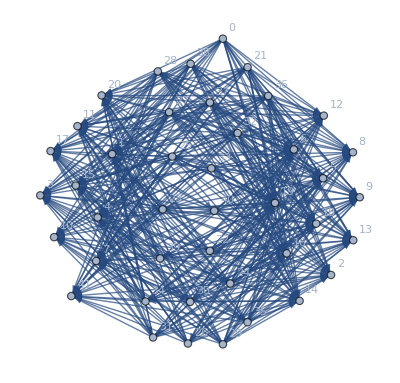

```mathematica
Graph[arcs,VertexLabels->"Name"]
```

Генерация начального маршрута

```mathematica
start=Nest[Insert[#,0,RandomInteger[{2,numberOfContainers}]]&,RandomSample[vertices1,UpTo[numberOfContainers]],numberOfVehicles-1]
```

{4,12,10,18,19,15,14,2,9,1,6,5,8,13,0,3,20,16,11,0,7,17}

```mathematica
distances=Join[{ConstantArray[0,numberOfContainers+1]},Transpose[Join[{ConstantArray[0,numberOfContainers]},Transpose[distanceMatrix]]]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0.156499,0.176401,3.02026,0.39246,2.58183,2.8044,2.496,2.67915,3.58678,3.15257,1.02728,3.4177,3.21591,2.14679,3.35059,3.23217,2.47967,1.80955,2.4877,1.80384},{0,2.56446,2.52492,3.91723,3.0409,2.38757,3.82092,1.1576,3.73655,1.55709,2.3034,2.3774,2.41693,4.09882,1.58844,4.13149,3.4293,0.224278,1.66074,0.211498,1.30449},{0,2.94508,2.89799,1.22602,3.25715,0.54411,1.26449,1.77576,1.25922,2.26002,0.929665,3.59893,1.10465,1.34582,1.38537,1.31338,0.503975,2.89579,3.68995,2.88345,1.85541},{0,3.24871,3.20122,3.6538,3.72936,2.0263,3.62017,0.960172,3.5659,0.493649,1.63975,3.2872,1.64507,3.80435,1.50663,3.79221,2.9633,1.25385,2.70171,1.23508,1.58397},{0,2.29779,2.24617,2.20798,2.72266,0.645284,2.14284,0.626349,2.0765,1.49225,0.8608,2.72806,1.10778,2.37881,0.237603,2.39802,1.69018,1.7077,2.61304,1.69553,0.75014},{0,3.028,2.9836,3.84672,3.51107,2.23424,3.78683,1.02197,3.71948,0.959817,1.96813,2.95949,2.01896,4.01135,1.56787,4.01737,3.23186,0.840739,2.29804,0.823047,1.48955},{0,2.14997,2.12957,4.42012,2.55298,3.11267,4.27352,2.05717,4.16768,2.6995,3.23262,1.5955,3.39898,4.61825,2.27268,4.68893,4.13589,0.991598,0.654138,1.0106,1.79957},{0,1.72978,1.68731,1.4704,1.99331,1.09072,1.29693,1.77839,1.18435,2.73623,1.78139,2.49142,2.0463,1.67339,1.22391,1.77535,1.54984,2.5408,2.82581,2.53613,1.36087},{0,2.79032,2.74426,3.55143,3.27307,1.94742,3.48714,0.72,3.41807,0.929074,1.73306,2.79186,1.81348,3.71873,1.26221,3.72904,2.95897,0.781776,2.21154,0.76275,1.19779},{0,3.69049,3.65147,0.704269,3.88316,1.73822,0.931083,2.98264,1.04112,3.40806,2.05921,4.47267,2.15036,0.595836,2.55615,0.42909,0.714472,4.08295,4.73353,4.07162,2.9824},{0,2.86657,2.83467,0.32216,2.98316,1.69733,0.123392,2.84492,0.147194,3.56864,2.29164,3.71217,2.48317,0.470434,2.31632,0.633978,1.15742,3.78781,4.13634,3.78063,2.60726},{0,0.97067,0.919026,2.5516,1.41328,1.66972,2.37702,1.48855,2.2621,2.58311,2.16887,1.49894,2.4278,2.75446,1.12897,2.852,2.49837,1.73398,1.74509,1.73586,0.803325},{0,1.78324,1.73174,2.43268,2.23058,1.08865,2.31848,0.711929,2.22833,1.79467,1.41981,2.16929,1.66267,2.62275,0.329923,2.67496,2.09158,1.41363,2.09022,1.40648,0.247487},{0,2.60786,2.5668,3.8476,3.08729,2.30021,3.75732,1.06091,3.67576,1.42991,2.19208,2.45959,2.29951,4.02668,1.51617,4.05504,3.33873,0.314544,1.77017,0.297612,1.26803},{0,1.6085,1.56306,3.10802,2.09157,1.79769,2.97459,0.960223,2.875,1.96281,2.02499,1.69293,2.23517,3.30328,0.974218,3.36665,2.80801,0.865541,1.40849,0.8663,0.473675},{0,0.368792,0.388366,3.4426,0.659684,2.80513,3.23505,2.48383,3.11077,3.5433,3.30346,0.522206,3.55828,3.64212,2.23601,3.76778,3.56343,2.23409,1.34475,2.24521,1.80803},{0,1.57931,1.5279,2.19537,1.99583,1.06438,2.05991,1.04848,1.96098,2.11229,1.55018,2.09443,1.81167,2.39201,0.563822,2.46119,1.97338,1.70605,2.17369,1.70109,0.525796},{0,1.19833,1.19375,2.25416,1.10388,2.40549,2.02316,2.82343,1.90226,3.88747,3.08649,2.07937,3.35438,2.42881,2.32744,2.5855,2.71852,3.18932,2.82022,3.1923,2.20137},{0,1.18943,1.16318,1.94935,1.30236,1.8889,1.72806,2.33159,1.60276,3.38119,2.56528,2.06504,2.8337,2.14094,1.81998,2.28225,2.28331,2.80343,2.65432,2.80418,1.74139},{0,1.10652,1.11962,2.65111,0.856486,2.76857,2.41956,3.07686,2.29996,4.1596,3.43694,1.92571,3.70645,2.82204,2.61213,2.98101,3.12163,3.31355,2.75919,3.31873,2.42156}}

```mathematica
simulatedAnnealing[points_,t_,α_,iter_,dist_]:=Module[{distanceMatrix=dist,numberOfVertices=Length[DeleteDuplicates@points],newt=t,v,start,distance,elem1,elem2,elems,newStart1,newStart2,newStart3,newDistance1,newDistance2,newDistance3,del,temp,starts,distances,minimal,pos},
v=Range@numberOfVertices;
start=points;
Do[distance=Total@Table[distanceMatrix⟦start⟦i⟧+1,start⟦i+1⟧+1⟧,{i,numberOfVertices-1}]+distanceMatrix⟦start⟦-1⟧+1,start⟦1⟧+1⟧;
elem1=RandomChoice[v];
elem2=RandomChoice[Delete[v,elem1]];
elems={elem1,elem2};
newStart1=start;
newStart1⟦Min@elems;;Max@elems⟧=Reverse@newStart1⟦Min@elems;;Max@elems⟧;
newDistance1=Total@Table[distanceMatrix⟦newStart1⟦i⟧+1,newStart1⟦i+1⟧+1⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart1⟦-1⟧+1,newStart1⟦1⟧+1⟧;
newStart2=start;
del=newStart2⟦elem1⟧;
newStart2=Delete[newStart2,elem1];
newStart2=Insert[newStart2,del,elem2];
newDistance2=Total@Table[distanceMatrix⟦newStart2⟦i⟧+1,newStart2⟦i+1⟧+1⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart2⟦-1⟧+1,newStart2⟦1⟧+1⟧;
newStart3=start;
temp=newStart3⟦elem2⟧;
newStart3⟦elem2⟧=newStart3⟦elem1⟧;
newStart3⟦elem1⟧=temp;
newDistance3=Total@Table[distanceMatrix⟦newStart3⟦i⟧+1,newStart3⟦i+1⟧+1⟧,{i,numberOfVertices-1}]+distanceMatrix⟦newStart3⟦-1⟧+1,newStart3⟦1⟧+1⟧;
starts={newStart1,newStart2,newStart3};
distances={newDistance1,newDistance2,newDistance3};
minimal=Min@distances;
pos=Position[distances,minimal]⟦1,1⟧;
start=If[Which[distance≥ minimal,True,distance< minimal,RandomReal[]<E^((-(minimal-distance))/newt)],starts⟦pos⟧,start];
newt=α newt,{k,iter}];{Min@{distance,minimal},start}]
```

```mathematica
solution=simulatedAnnealing[start,200,0.9,5000,distances]
```

General::munfl: Exp[-774.227] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-956.782] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-737.402] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{13.4842,{20,2,19,8,5,10,15,0,13,14,7,18,0,6,12,11,3,16,1,4,9,17}}

```mathematica
distances//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.156499 | 0.176401 | 3.02026 | 0.39246 | 2.58183 | 2.8044 | 2.496 | 2.67915 | 3.58678 | 3.15257 | 1.02728 | 3.4177 | 3.21591 | 2.14679 | 3.35059 | 3.23217 | 2.47967 | 1.80955 | 2.4877 | 1.80384
0 | 2.56446 | 2.52492 | 3.91723 | 3.0409 | 2.38757 | 3.82092 | 1.1576 | 3.73655 | 1.55709 | 2.3034 | 2.3774 | 2.41693 | 4.09882 | 1.58844 | 4.13149 | 3.4293 | 0.224278 | 1.66074 | 0.211498 | 1.30449
0 | 2.94508 | 2.89799 | 1.22602 | 3.25715 | 0.54411 | 1.26449 | 1.77576 | 1.25922 | 2.26002 | 0.929665 | 3.59893 | 1.10465 | 1.34582 | 1.38537 | 1.31338 | 0.503975 | 2.89579 | 3.68995 | 2.88345 | 1.85541
0 | 3.24871 | 3.20122 | 3.6538 | 3.72936 | 2.0263 | 3.62017 | 0.960172 | 3.5659 | 0.493649 | 1.63975 | 3.2872 | 1.64507 | 3.80435 | 1.50663 | 3.79221 | 2.9633 | 1.25385 | 2.70171 | 1.23508 | 1.58397
0 | 2.29779 | 2.24617 | 2.20798 | 2.72266 | 0.645284 | 2.14284 | 0.626349 | 2.0765 | 1.49225 | 0.8608 | 2.72806 | 1.10778 | 2.37881 | 0.237603 | 2.39802 | 1.69018 | 1.7077 | 2.61304 | 1.69553 | 0.75014
0 | 3.028 | 2.9836 | 3.84672 | 3.51107 | 2.23424 | 3.78683 | 1.02197 | 3.71948 | 0.959817 | 1.96813 | 2.95949 | 2.01896 | 4.01135 | 1.56787 | 4.01737 | 3.23186 | 0.840739 | 2.29804 | 0.823047 | 1.48955
0 | 2.14997 | 2.12957 | 4.42012 | 2.55298 | 3.11267 | 4.27352 | 2.05717 | 4.16768 | 2.6995 | 3.23262 | 1.5955 | 3.39898 | 4.61825 | 2.27268 | 4.68893 | 4.13589 | 0.991598 | 0.654138 | 1.0106 | 1.79957
0 | 1.72978 | 1.68731 | 1.4704 | 1.99331 | 1.09072 | 1.29693 | 1.77839 | 1.18435 | 2.73623 | 1.78139 | 2.49142 | 2.0463 | 1.67339 | 1.22391 | 1.77535 | 1.54984 | 2.5408 | 2.82581 | 2.53613 | 1.36087
0 | 2.79032 | 2.74426 | 3.55143 | 3.27307 | 1.94742 | 3.48714 | 0.72 | 3.41807 | 0.929074 | 1.73306 | 2.79186 | 1.81348 | 3.71873 | 1.26221 | 3.72904 | 2.95897 | 0.781776 | 2.21154 | 0.76275 | 1.19779
0 | 3.69049 | 3.65147 | 0.704269 | 3.88316 | 1.73822 | 0.931083 | 2.98264 | 1.04112 | 3.40806 | 2.05921 | 4.47267 | 2.15036 | 0.595836 | 2.55615 | 0.42909 | 0.714472 | 4.08295 | 4.73353 | 4.07162 | 2.9824
0 | 2.86657 | 2.83467 | 0.32216 | 2.98316 | 1.69733 | 0.123392 | 2.84492 | 0.147194 | 3.56864 | 2.29164 | 3.71217 | 2.48317 | 0.470434 | 2.31632 | 0.633978 | 1.15742 | 3.78781 | 4.13634 | 3.78063 | 2.60726
0 | 0.97067 | 0.919026 | 2.5516 | 1.41328 | 1.66972 | 2.37702 | 1.48855 | 2.2621 | 2.58311 | 2.16887 | 1.49894 | 2.4278 | 2.75446 | 1.12897 | 2.852 | 2.49837 | 1.73398 | 1.74509 | 1.73586 | 0.803325
0 | 1.78324 | 1.73174 | 2.43268 | 2.23058 | 1.08865 | 2.31848 | 0.711929 | 2.22833 | 1.79467 | 1.41981 | 2.16929 | 1.66267 | 2.62275 | 0.329923 | 2.67496 | 2.09158 | 1.41363 | 2.09022 | 1.40648 | 0.247487
0 | 2.60786 | 2.5668 | 3.8476 | 3.08729 | 2.30021 | 3.75732 | 1.06091 | 3.67576 | 1.42991 | 2.19208 | 2.45959 | 2.29951 | 4.02668 | 1.51617 | 4.05504 | 3.33873 | 0.314544 | 1.77017 | 0.297612 | 1.26803
0 | 1.6085 | 1.56306 | 3.10802 | 2.09157 | 1.79769 | 2.97459 | 0.960223 | 2.875 | 1.96281 | 2.02499 | 1.69293 | 2.23517 | 3.30328 | 0.974218 | 3.36665 | 2.80801 | 0.865541 | 1.40849 | 0.8663 | 0.473675
0 | 0.368792 | 0.388366 | 3.4426 | 0.659684 | 2.80513 | 3.23505 | 2.48383 | 3.11077 | 3.5433 | 3.30346 | 0.522206 | 3.55828 | 3.64212 | 2.23601 | 3.76778 | 3.56343 | 2.23409 | 1.34475 | 2.24521 | 1.80803
0 | 1.57931 | 1.5279 | 2.19537 | 1.99583 | 1.06438 | 2.05991 | 1.04848 | 1.96098 | 2.11229 | 1.55018 | 2.09443 | 1.81167 | 2.39201 | 0.563822 | 2.46119 | 1.97338 | 1.70605 | 2.17369 | 1.70109 | 0.525796
0 | 1.19833 | 1.19375 | 2.25416 | 1.10388 | 2.40549 | 2.02316 | 2.82343 | 1.90226 | 3.88747 | 3.08649 | 2.07937 | 3.35438 | 2.42881 | 2.32744 | 2.5855 | 2.71852 | 3.18932 | 2.82022 | 3.1923 | 2.20137
0 | 1.18943 | 1.16318 | 1.94935 | 1.30236 | 1.8889 | 1.72806 | 2.33159 | 1.60276 | 3.38119 | 2.56528 | 2.06504 | 2.8337 | 2.14094 | 1.81998 | 2.28225 | 2.28331 | 2.80343 | 2.65432 | 2.80418 | 1.74139
0 | 1.10652 | 1.11962 | 2.65111 | 0.856486 | 2.76857 | 2.41956 | 3.07686 | 2.29996 | 4.1596 | 3.43694 | 1.92571 | 3.70645 | 2.82204 | 2.61213 | 2.98101 | 3.12163 | 3.31355 | 2.75919 | 3.31873 | 2.42156)

```mathematica
route={0}~Join~solution⟦2⟧~Join~{0}
```

{0,20,2,19,8,5,10,15,0,13,14,7,18,0,6,12,11,3,16,1,4,9,17,0}

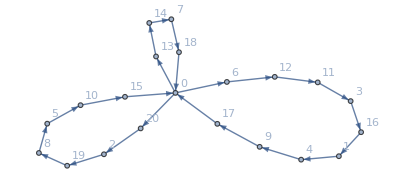

```mathematica
Graph[DirectedEdge@@@Table[{route⟦i⟧,route⟦i+1⟧},{i,numberOfContainers+numberOfVehicles}],VertexLabels->"Name"]
```

Генерация переменных

```mathematica
varsYPV1=y@@@pairsVertices1;
varsYPV2=y@@@pairsVertices2;

varsS=s/@Range[2numberOfContainers];
varsSOut=s[0,#]&/@Range[numberOfVehicles];
varsSIn=s[2numberOfContainers+1,#]&/@Range[numberOfVehicles];
```

```mathematica
vars=Join[varsS,varsSOut,varsSIn,varsYPV1,varsYPV2,{umax}]
```

{s[1],s[2],s[3],s[4],s[5],s[6],s[7],s[8],s[9],s[10],s[11],s[12],s[13],s[14],s[15],s[16],s[17],s[18],s[19],s[20],s[21],s[22],s[23],s[24],s[25],s[26],s[27],s[28],s[29],s[30],s[31],s[32],s[33],s[34],s[35],s[36],s[37],s[38],s[39],s[40],s[0,1],s[0,2],s[0,3],s[41,1],s[41,2],s[41,3],y[6,16],y[5,8],y[5,10],y[2,16],y[1,10],y[19,20],y[5,12],y[11,20],y[3,18],y[27,32],y[23,26],y[24,28],y[26,31],y[21,40],y[23,24],y[23,35],y[33,40],y[30,31],umax}

Целевая функция

```mathematica
objFun1=vars/.{s[0,_]->-1,s[2numberOfContainers+1,_]->1,_x|_s|_y|umax->0};
objFun2=Replace[vars,{umax->1,_->0},1];
```

```mathematica
Clear[varsXOut,varsXIn,varsXClients]
```

```mathematica
out=Partition[Flatten@Outer[{Sequence@@#1,#2}&,startArcs,Range@numberOfVehicles,1],3];
in=Partition[Flatten@Outer[{Sequence@@#1,#2}&,endArcs,Range@numberOfVehicles,1],3];
allArcs=Join[out,in]
```

{{0,1,1},{0,1,2},{0,1,3},{0,2,1},{0,2,2},{0,2,3},{0,3,1},{0,3,2},{0,3,3},{0,4,1},{0,4,2},{0,4,3},{0,5,1},{0,5,2},{0,5,3},{0,6,1},{0,6,2},{0,6,3},{0,7,1},{0,7,2},{0,7,3},{0,8,1},{0,8,2},{0,8,3},{0,9,1},{0,9,2},{0,9,3},{0,10,1},{0,10,2},{0,10,3},{0,11,1},{0,11,2},{0,11,3},{0,12,1},{0,12,2},{0,12,3},{0,13,1},{0,13,2},{0,13,3},{0,14,1},{0,14,2},{0,14,3},{0,15,1},{0,15,2},{0,15,3},{0,16,1},{0,16,2},{0,16,3},{0,17,1},{0,17,2},{0,17,3},{0,18,1},{0,18,2},{0,18,3},{0,19,1},{0,19,2},{0,19,3},{0,20,1},{0,20,2},{0,20,3},{21,41,1},{21,41,2},{21,41,3},{22,41,1},{22,41,2},{22,41,3},{23,41,1},{23,41,2},{23,41,3},{24,41,1},{24,41,2},{24,41,3},{25,41,1},{25,41,2},{25,41,3},{26,41,1},{26,41,2},{26,41,3},{27,41,1},{27,41,2},{27,41,3},{28,41,1},{28,41,2},{28,41,3},{29,41,1},{29,41,2},{29,41,3},{30,41,1},{30,41,2},{30,41,3},{31,41,1},{31,41,2},{31,41,3},{32,41,1},{32,41,2},{32,41,3},{33,41,1},{33,41,2},{33,41,3},{34,41,1},{34,41,2},{34,41,3},{35,41,1},{35,41,2},{35,41,3},{36,41,1},{36,41,2},{36,41,3},{37,41,1},{37,41,2},{37,41,3},{38,41,1},{38,41,2},{38,41,3},{39,41,1},{39,41,2},{39,41,3},{40,41,1},{40,41,2},{40,41,3}}

Ограничения

```mathematica
con5={s@#⟦1⟧-s@#⟦2⟧+K*#,{K-distanceMatrix[#],-1}}&/@allArcs;
```

```mathematica
con6={s[0,#⟦3⟧]-s@#⟦2⟧+K*#,{K-ϵ,-1}}&/@out;
```

```mathematica
con7={s@#⟦1⟧-s[2numberOfContainers+1,#⟦3⟧]+K*#,{K-ϵ,-1}}&/@in;
```

```mathematica
con8={s[0,#⟦1,3⟧]-K*Total[#],{0,-1}}&/@GatherBy[out,Last];
```

```mathematica
con9={s[#⟦2⟧]-s[#⟦1⟧],{δ1,1}}&/@Flatten[Partition[Reverse@#,2,1]&/@stacks,1];
```

```mathematica
con10={s[#⟦2⟧]-s[#⟦1⟧]+K #,{δ2,1}}&/@Join[varsYPV1,varsYPV2];
```

```mathematica
con11={s[#⟦1⟧]-s[#⟦2⟧]-K #,{δ2-K,1}}&/@Join[varsYPV1,varsYPV2];
```

```mathematica
con12={#,{0,1}}&/@(umax-varsSIn);
```

```mathematica
con13={s[0,#⟦1,-1⟧]-K Total@#,{0,-1}}&/@GatherBy[out,Last];
```

```mathematica
getVector=Last[CoefficientArrays[#,vars]]&;
```

```mathematica
constraints=Join[con5,con6,con7,con8,con9,con10,con11,con12,con13];
```

```mathematica
m=Last@CoefficientArrays[constraints⟦All,1⟧,vars]
```

CoefficientArrays::eelist: The first argument {{0.+s[0]-s[1],436.065+s[0]-s[1],436.065+s[0]-s[1]},{0.+s[0]-s[1],436.065+s[0]-s[1],872.131+s[0]-s[1]},{0.+s[0]-s[1],436.065+s[0]-s[1],1308.2+s[0]-s[1]},{0.+s[0]-s[2],872.131+s[0]-s[2],436.065+s[0]-s[2]},«4»,{0.+s[0]-s[3],1308.2+s[0]-s[3],1308.2+s[0]-s[3]},{0.+s[0]-s[4],1744.26+s[0]-s[4],436.065+s[0]-s[4]},«293»} should be a list of polynomials or equations.

{s[1],s[2],s[3],s[4],s[5],s[6],s[7],s[8],s[9],s[10],s[11],s[12],s[13],s[14],s[15],s[16],s[17],s[18],s[19],s[20],s[21],s[22],s[23],s[24],s[25],s[26],s[27],s[28],s[29],s[30],s[31],s[32],s[33],s[34],s[35],s[36],s[37],s[38],s[39],s[40],s[0,1],s[0,2],s[0,3],s[41,1],s[41,2],s[41,3],y[6,16],y[5,8],y[5,10],y[2,16],y[1,10],y[19,20],y[5,12],y[11,20],y[3,18],y[27,32],y[23,26],y[24,28],y[26,31],y[21,40],y[23,24],y[23,35],y[33,40],y[30,31],umax}

```mathematica
b=constraints⟦All,2⟧;
```

```mathematica
lu=Join[
ConstantArray[{0,1},Length[allArcs]+Length[out]+Length[in]],ConstantArray[{0,Total[distanceMatrix,2]},Length[varsS]+Length[varsSOut]+Length[varsSIn]],
ConstantArray[{0,1},Length[varsYPV1]+Length[varsYPV2]],{{0,Total[distanceMatrix,2]}}];
```

```mathematica
domain=Join[
ConstantArray[Integers,Length[allArcs]+Length[out]+Length[in]],
ConstantArray[Reals,Length[varsS]+Length[varsSOut]+Length[varsSIn]],
ConstantArray[Integers,Length[varsYPV1]+Length[varsYPV2]],
{Reals}];
```